```mathematica
μ=0.62;
γ=5/3;
```

```mathematica
years=365.25*86400;
tEnd=10^3 years;
tref:=1/Ω[Rper,zper]
```

```mathematica
rper=0.7Rsun;
θper=45*Pi/180;
kRoss=21.1;
χ=(16*T[Rper,zper]^3*sigmaSB*(γ-1)*μ*mP)/(3*kRoss*ρ[Rper,zper]^2*kB);  (*this is what Goldreich and Schubert call χ*)
ξradiative = (γ-1)*χ;    (*this is what Balbus and Schaan call ξrad*)

ν=23;   (*from Menou&Balbus2004*)

η=596;     (*from Menou&Balbus2004*)

δvϕsol[t_]:=-(δvRsol[t]*kR[t]+δvzsol[t]*kz[t])/kϕ0
```

```mathematica
ξradiative = (γ-1)*χ ; 
ν=23;  
η=596;    
kR0=2.1*10^-4;
kϕ0=4.2*10^-7;
kz0=1.3*10^-5;
kR[t_]=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]=kϕ0;
kz[t_]=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];

k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);

kdotvA=0.01Ω[Rper,zper];

vR0=-(kz0/kR0);
vϕ0=0;
vz0=1;

δρ0=0;
δCR0=0;
δCz0=0;

vmod0=√(vR0^2+vz0^2);
TimeConstrained[SolveTheSystem,5];
```

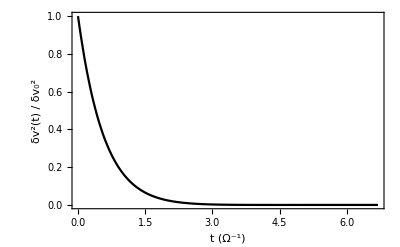

```mathematica
Graphico3=Plot[(δvRsol[tref*t]^2+δvϕsol[t]^2+δvzsol[tref*t]^2)/vmod0^2,{t,0,0.8(tEnd/tref)/(10^4)},PlotStyle->Black,PlotRange->Full,Frame->True,FrameLabel->{"t (Ω^-1)","δv^2(t) / δv_0^2"(*,"ξ_rad = ξ_(rad⊙),  ν = ν_⊙,  η = η_⊙"*)},BaseStyle->{FontWeight->"Plain",FontSize->14},FrameStyle->Black, LabelStyle -> Black]
Graphico3bis=Plot[(δvRsol[tref*t]^2+δvϕsol[t]^2+δvzsol[tref*t]^2)/vmod0^2,{t,0,0.8(tEnd/tref)/(10^4)},PlotStyle->Directive[Gray, Dashed],PlotRange->Full,Frame->True,FrameLabel->{"t (Ω^-1)","δv^2(t) / δv_0^2"(*,"ξ_rad = ξ_(rad⊙),  ν = ν_⊙,  η = η_⊙"*)},BaseStyle->{FontWeight->"Plain",FontSize->14},FrameStyle->Black, LabelStyle -> Black];
```

```mathematica
ξradiative = (γ-1)*χ ; 
ν=2;  
η=596;     
kR0=2.1*10^-4;
kϕ0=4.2*10^-7;
kz0=1.3*10^-5;
kR[t_]=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]=kϕ0;
kz[t_]=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];

k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);

kdotvA=0.01Ω[Rper,zper];

vR0=-(kz0/kR0);
vϕ0=0;
vz0=1;

δρ0=0;
δCR0=0;
δCz0=0;

vmod0=√(vR0^2+vz0^2);
TimeConstrained[SolveTheSystem,5];
```

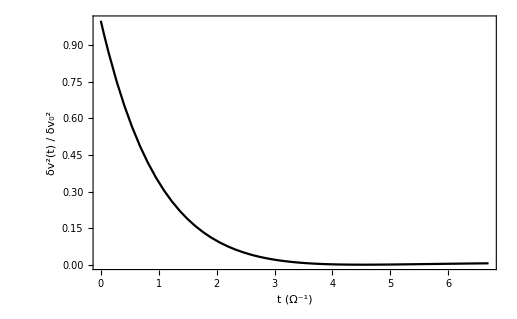

```mathematica
Graphico4=Plot[(δvRsol[tref*t]^2+δvϕsol[t]^2+δvzsol[tref*t]^2)/vmod0^2,{t,0,0.8(tEnd/tref)/(10^4)},PlotStyle->Black,PlotRange->Full,Frame->True,FrameLabel->{"t (Ω^-1)","δv^2(t) / δv_0^2"(*,"ξ_rad = ξ_(rad⊙),  ν = 0.1ν_⊙,  η = η_⊙"*)},BaseStyle->{FontWeight->"Plain",FontSize->14},FrameStyle->Black, LabelStyle -> Black]
```

```mathematica
ξradiative = (γ-1)*χ ; 
ν=23;  
η=596;    
kR0=2.1*10^-4;
kϕ0=4.2*10^-7;
kz0=1.3*10^-5;
kR[t_]=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]=kϕ0;
kz[t_]=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];

k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);

kdotvA=100Ω[Rper,zper];

vR0=-(kz0/kR0);
vϕ0=0;
vz0=1;

δρ0=0;
δCR0=0;
δCz0=0;

vmod0=√(vR0^2+vz0^2);
TimeConstrained[SolveTheSystem,5];
```

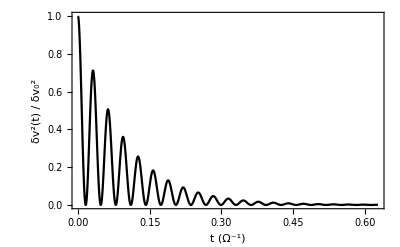

```mathematica
Graphico6=Plot[(δvRsol[tref*t]^2+δvϕsol[t]^2+δvzsol[tref*t]^2)/vmod0^2,{t,0,0.75(tEnd/tref)/(10^5)},PlotStyle->Black,PlotRange->Full,Frame->True,FrameLabel->{"t (Ω^-1)","δv^2(t) / δv_0^2"(*, "k·v_A = 10^2Ω,  ξ_rad = ξ_(rad⊙),  ν = ν_⊙,  η = η_⊙"*)},BaseStyle->{FontWeight->"Plain",FontSize->14},FrameStyle->Black,LabelStyle->Black]
```

```mathematica
ξradiative = (γ-1)*χ ; 
ν=23;  
η=0;     
kR0=2.1*10^-4;
kϕ0=4.2*10^-7;
kz0=1.3*10^-5;
kR[t_]=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]=kϕ0;
kz[t_]=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];

k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);

kdotvA=100Ω[Rper,zper];

vR0=-(kz0/kR0);
vϕ0=0;
vz0=1;

δρ0=0;
δCR0=0;
δCz0=0;

vmod0=√(vR0^2+vz0^2);
TimeConstrained[SolveTheSystem,5];
```

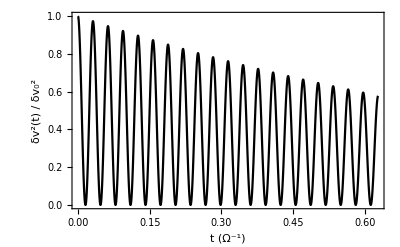

```mathematica
Graphico7=Plot[(δvRsol[tref*t]^2+δvϕsol[t]^2+δvzsol[tref*t]^2)/vmod0^2,{t,0,0.75(tEnd/tref)/(10^5)},PlotStyle->Black,PlotRange->Full,Frame->True,FrameLabel->{"t (Ω^-1)","δv^2(t) / δv_0^2"(*,"k·v_A = 10^2Ω,  ξ_rad = ξ_(rad⊙),  ν = ν_⊙,  η = 0.1η_⊙"*)},BaseStyle->{FontWeight->"Plain",FontSize->14},FrameStyle->Black, LabelStyle -> Black]
```

```mathematica
θper=17*Pi/36;
ξradiative = (γ-1)*χ ; 
ν=23;  
η=596;    
kR0=8.7*10^-9;
kϕ0=1.52*10^-10;
kz0=4.85*10^-9;
kR[t_]=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]=kϕ0;
kz[t_]=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];

k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);

kdotvA=0.01Ω[Rper,zper];

vR0=-(kz0/kR0);
vϕ0=0;
vz0=1;

δρ0=0;
δCR0=0;
δCz0=0;

vmod0=√(vR0^2+vz0^2);
SolveTheSystem;
```

```mathematica
(*meanδvSqsol[t0_]:=1/400 Total[Table[(δvRsol[t0+1/400*k*Ω[Rper,zper]^-1]^2+δvϕsol[t0+1/400*k*Ω[Rper,zper]^-1]^2+δvzsol[t0+1/400*k*Ω[Rper,zper]^-1]^2)/vmod0^2,{k,1,400}]]

Graphico8=Plot[(δvRsol[tref*t]^2+δvϕsol[t]^2+δvzsol[tref*t]^2)/vmod0^2,{t,0,0.025(tEnd/tref)/(1.5*10^4)},PlotStyle->Directive[Black],PlotRange->Full,Frame->True,FrameLabel->{"t (Ω^-1)","δv^2(t) / δv_0^2"(*,"ξ_rad = ξ_(rad⊙),  ν = ν_⊙,  η = η_⊙"*)},FrameStyle->Black,BaseStyle->{FontWeight->"Plain",FontSize->14}]*)
```

```mathematica
(*δvSqList=Table[{t,meanδvSqsol[t*tref]},{t,0,(tEnd/tref)/(1.5*10^2),0.5}];
meanδvSqN=Interpolation[δvSqList,InterpolationOrder->8]
Graphico9=Plot[meanδvSqN[t],{t,0,(tEnd/tref)/(1.5*10^2)},PlotStyle->Directive[Black,Thickness[0.01]],PlotRange->Full,Frame->True,FrameLabel->{"t (Ω^-1)",OverBar["δv^2(t) / δv_0^2"]},FrameStyle->Black,BaseStyle->{FontWeight->"Plain",FontSize->14}]*)
(*Graphico9=ListPlot[δvSqList,Joined->True,PlotStyle->Thickness[0.01],PlotRange->Full,Frame->True,FrameLabel->{"t (Ω^-1)",OverBar["δv^2(t) / δv_0^2"],"ξ_rad = ξ_(rad⊙),  ν = ν_⊙,  η = η_⊙"},FrameStyle->Black,BaseStyle->{FontWeight->"Plain",FontSize->14}]*)
```

```mathematica
(*Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Stability - Project 2\\NiceExamples\\pic3.png",Graphico3,ImageResolution->180];
Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Stability - Project 2\\NiceExamples\\pic4.png",Graphico4,ImageResolution->180];
Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Stability - Project 2\\NiceExamples\\pic6.png",Graphico6,ImageResolution->180];*)
(*Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Stability - Project 2\\NiceExamples\\pic7.png",Graphico7,ImageResolution->180];*)
(*Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Stability - Project 2\\NiceExamples\\pic8.png",Graphico8,ImageResolution->180];
Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Stability - Project 2\\NiceExamples\\pic9.png",Graphico9,ImageResolution->180];*)
```

```mathematica
(*Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Stability - Project 2\\NiceExamples\\pic4bis.png",Show[Graphico3bis, Graphico4],ImageResolution->180];*)
```